```mathematica
Import[StringJoin[Characters[NotebookFileName[]][[;;-12]]]<>"pce.m"]
```

## Función Erase para borrar y conseguir canales PCE de menor cantidad de componentes:

```mathematica
Erase[EigInfo_,PCEfrom_,invariantComponents_]:=Module[{dimPCE},
dimPCE=Length[Dimensions[PCEfrom][[2;;]]];
If[Count[#//Flatten,1]==invariantComponents,#,Nothing]&/@
DeleteDuplicates[
Flatten[
Table[
DeleteDuplicates[ReplacePart[PCEfrom[[i]]+#-ConstantArray[1,ConstantArray[4,dimPCE]],#->0&/@Position[PCEfrom[[i]]+#-ConstantArray[1,ConstantArray[4,dimPCE]],-1]]&/@EigInfo]
,{i,Length[PCEfrom]}]
,1]
]
]
```

## Importar datos:

```mathematica
twoQ=ToExpression[Import["/home/jadeleon/Documents/pce/results/2qubits.dat","List"]];
```

```mathematica
threeQ=Flatten[ToExpression[Import["/home/jadeleon/Documents/pce/results/3qubits.dat","List"]],1];
```

## Cómo funciona Erase[]

```mathematica
PCEgenerators[n_]:=Module[{a},
a={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};
DiagonalMatrix[#]&/@ReplacePart[tensorPower[a,2],Position[tensorPower[a,2],-1]->0][[2;;]]
]
```

```mathematica
Diagonal/@PCEgenerators[2]
```

{{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1},{1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0},{1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1},{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0},{1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1},{1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0},{1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0},{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1}}

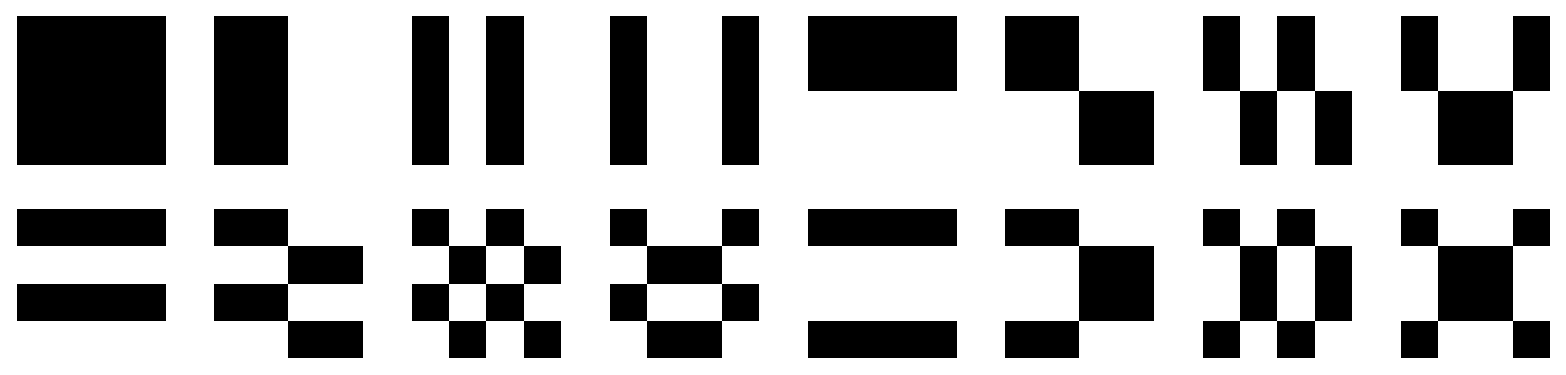

```mathematica
ArrayReshape[{ArrayPlot[ConstantArray[1,{4,4}]]}~Join~(ArrayPlot/@ArrayReshape[Diagonal/@PCEgenerators[2],{15,4,4}]),{2,8}]//GraphicsGrid
```

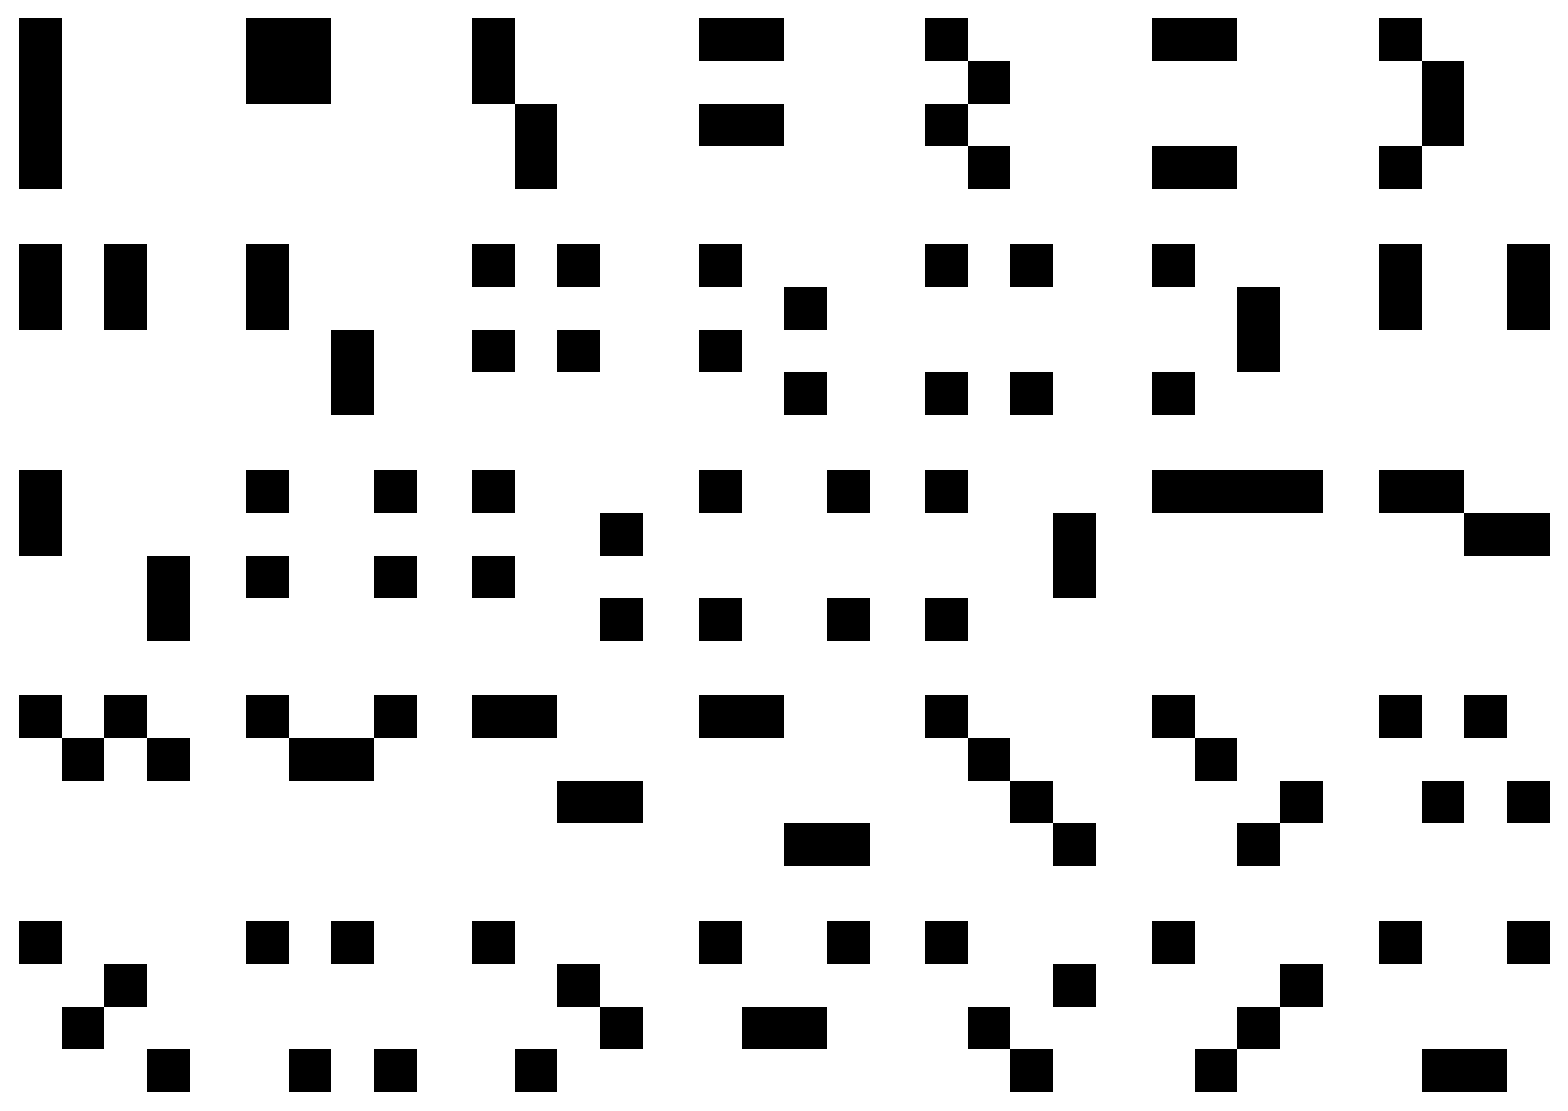

```mathematica
ArrayReshape[ArrayPlot/@Erase[ArrayReshape[Diagonal/@PCEgenerators[2],{15,4,4}],ArrayReshape[Diagonal/@PCEgenerators[2],{15,4,4}],4],{5,7}]//GraphicsGrid
```

```mathematica
q2c8=twoQ[[2;;]];
```


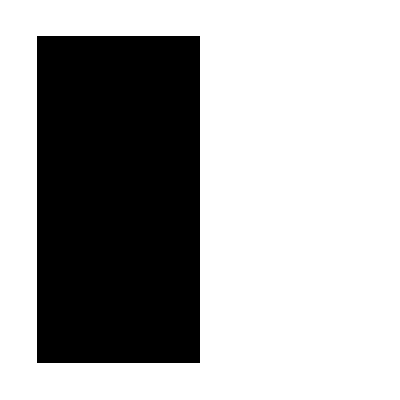
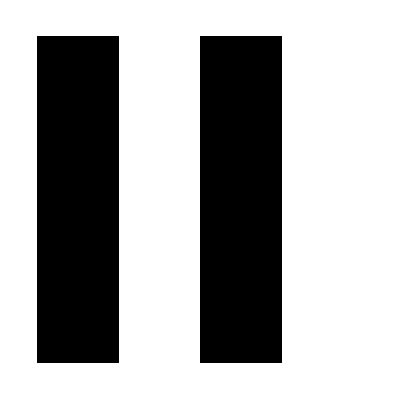
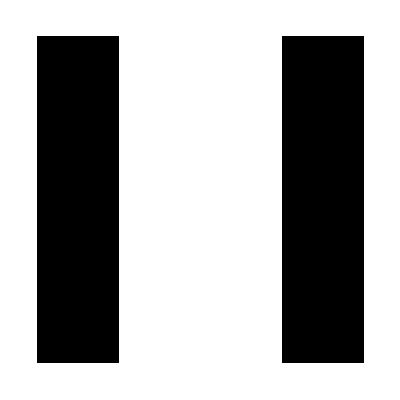
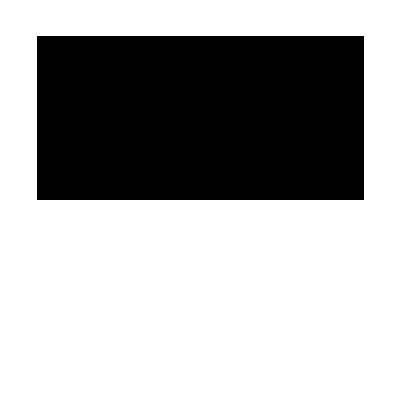
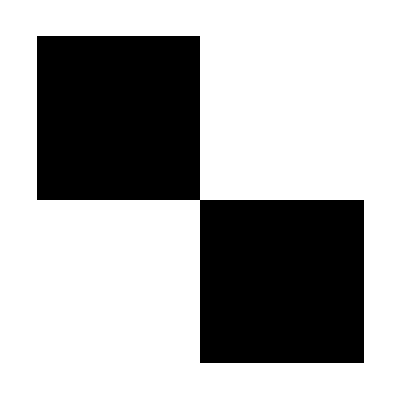
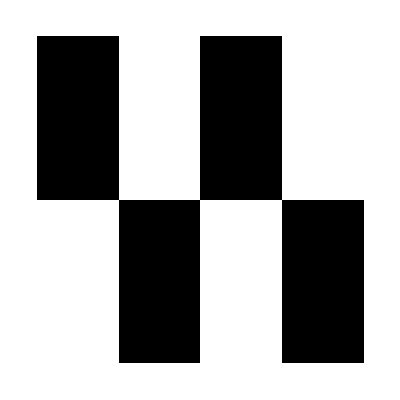
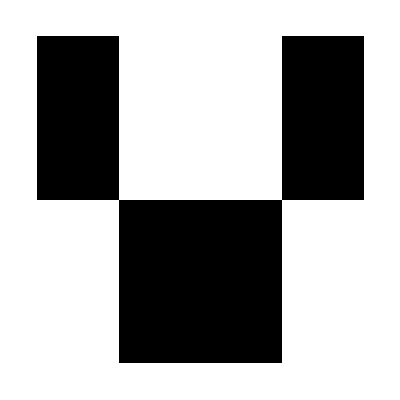
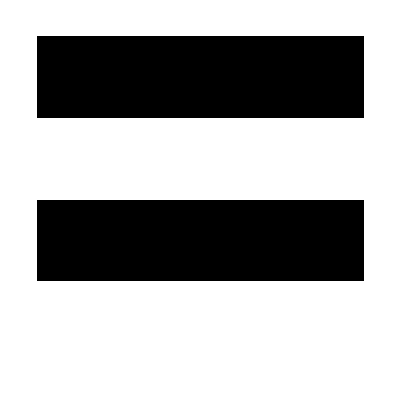

```mathematica
ArrayPlot/@twoQ
```

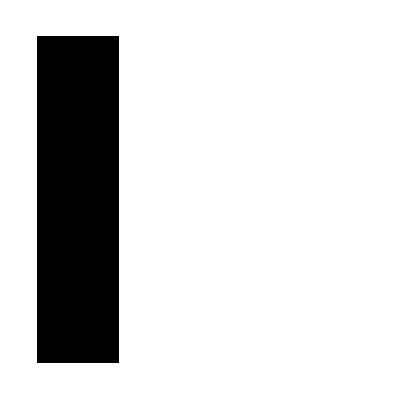
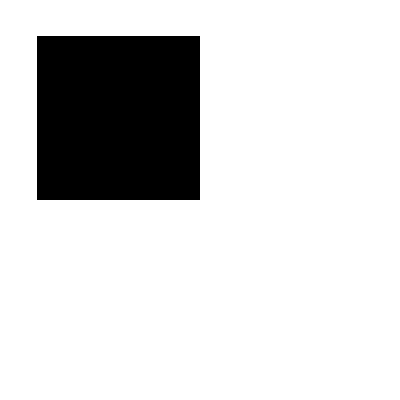
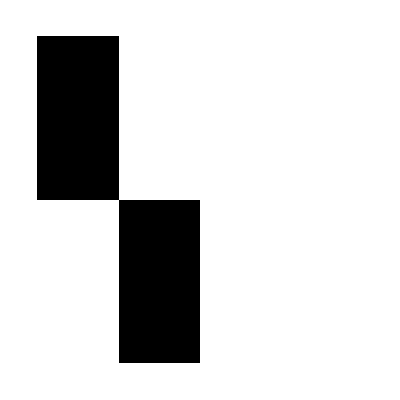
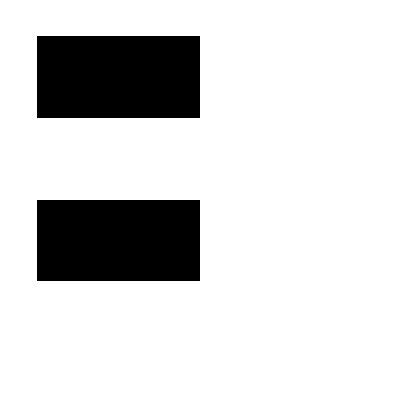
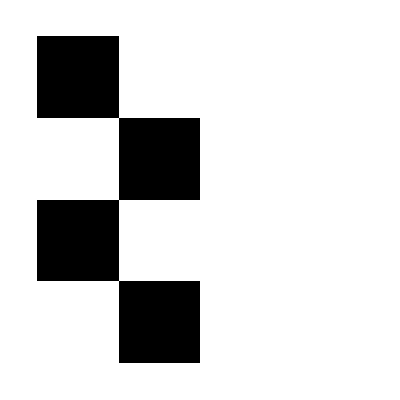
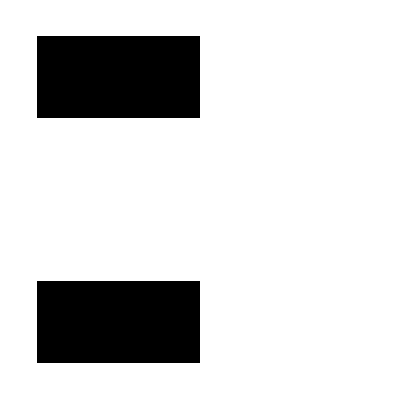
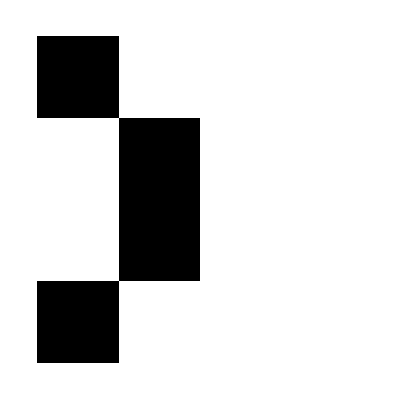
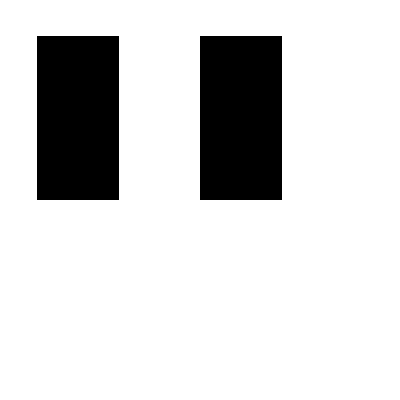

```mathematica
ArrayPlot[#]&/@Erase[q2c8,q2c8,4]
```

```mathematica
ArrayReshape[{ArrayPlot[{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]}~Join~(ArrayPlot/@Erase[q2c8,Erase[q2c8,q2c8,4],2]),{2,8}]//GraphicsGrid
```

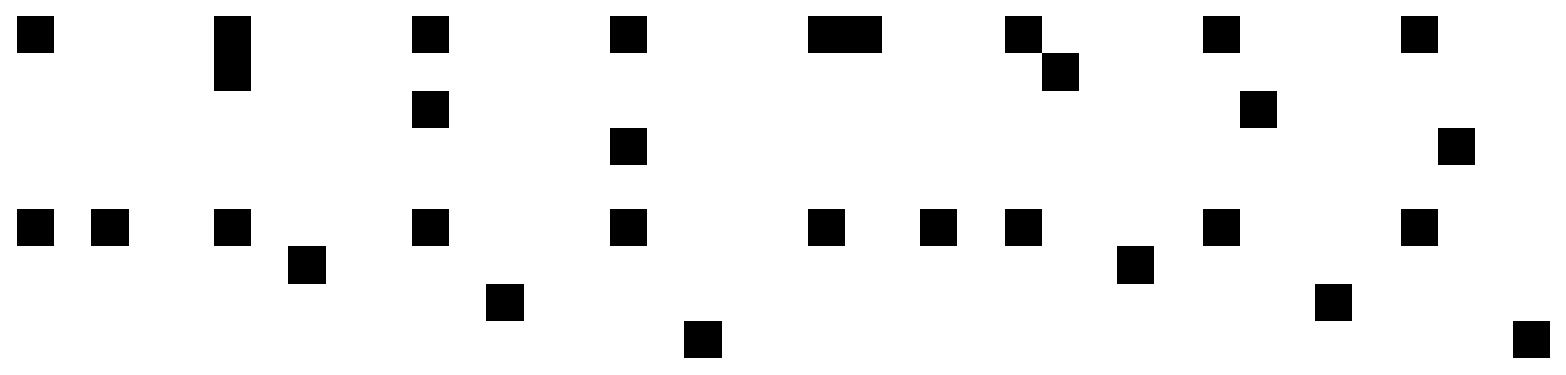

-Graphics-

```mathematica
|
```

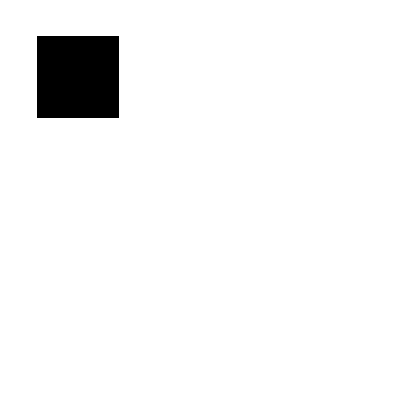

```mathematica
ArrayPlot/@Erase[q2c8,Erase[q2c8,Erase[q2c8,q2c8,4],2],1]
```

## 3 qubits

```mathematica
Needs["Quantum`"]
```

Pauli::shdw: Symbol Pauli appears in multiple contexts {Quantum`,quantumJA`}; definitions in context Quantum` may shadow or be shadowed by other definitions.

Reshuffle::shdw: Symbol Reshuffle appears in multiple contexts {Quantum`,quantumJA`}; definitions in context Quantum` may shadow or be shadowed by other definitions.

La función Cube3q[] toma por argumento los elementos de la diagonal de la operación PCE

```mathematica
Cube3q[threeQ[[15]]//Flatten]
```

-Graphics3D-

```mathematica
q3c32=threeQ[[2;;]];
```

```mathematica
q3c16=Erase[q3c32,q3c32,16];q3c16//Length
```

651

```mathematica
q3c8=Erase[q3c32,q3c16,8];q3c8//Length
```

1395

```mathematica
q3c4=Erase[q3c32,q3c8,4];q3c4//Length
```

651

```mathematica
q3c2=Erase[q3c32,q3c4,2];q3c2//Length
```

63

```mathematica
q3c1=Erase[q3c32,q3c2,1];q3c1//Length
```

1

```mathematica
representativos={};AppendTo[representativos,ThreeQ[[1+1]]];
```

```mathematica
AppendTo[representativos,ThreeQ[[60]]]
```

{{{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,0,0}},{{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,0,0}},{{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1}},{{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1}}},{{{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,0,0}},{{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1}},{{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,0,0}},{{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1}}},{{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{{0,0,1,1},{0,0,1,1},{1,1,0,0},{1,1,0,0}},{{0,0,1,1},{0,0,1,1},{1,1,0,0},{1,1,0,0}}},{{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{{0,0,1,1},{0,0,1,1},{1,1,0,0},{1,1,0,0}},{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{{0,0,1,1},{0,0,1,1},{1,1,0,0},{1,1,0,0}}},{{{1,0,1,0},{0,1,0,1},{0,1,0,1},{1,0,1,0}},{{0,1,0,1},{1,0,1,0},{1,0,1,0},{0,1,0,1}},{{0,1,0,1},{1,0,1,0},{1,0,1,0},{0,1,0,1}},{{1,0,1,0},{0,1,0,1},{0,1,0,1},{1,0,1,0}}}}

```mathematica
Cube3q[#//Flatten]&/@ThreeQ[[46;;63]]
```

```mathematica
Cube3q[#//Flatten]&/@Erase[representativos[[1;;4]],{representativos[[1]]},16]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Cube3q[#//Flatten]&/@Erase[representativos,{representativos[[3]]},16][[4;;6]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Cube3q[#//Flatten]&/@Erase[representativos,{representativos[[5]]},16][[6]]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
prueba=(Transpose[Erase[representativos,{representativos[[5]]},16][[6]],#]&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{1,2,3}]));
```

```mathematica
Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}])
```

{{1,2,3,4},{1,3,4,2},{1,4,2,3}}

```mathematica
(If[Signature[#]==1,#,Nothing]&/@Permutations[{1,2,3}])
```

{{1,2,3},{2,3,1},{3,1,2}}

```mathematica
Cube3q[Transpose[ThreeQ[[7]],{2,1,3}]//Flatten]
```

-Graphics3D-

```mathematica
{Cube3q[ThreeQ[[7]]//Flatten],Cube3q[ThreeQ[[7,{1,2,3,4},{1,2,3,4},{1,4,3,2}]]//Flatten]}
```

{-Graphics3D-,-Graphics3D-}

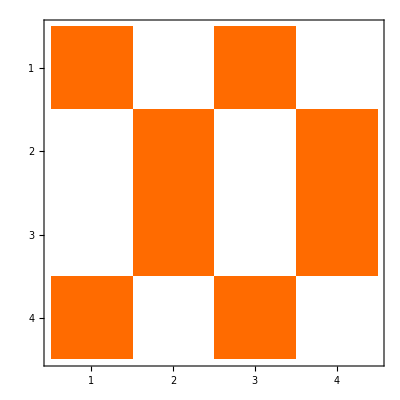
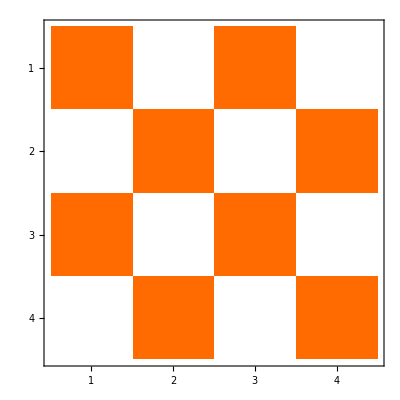
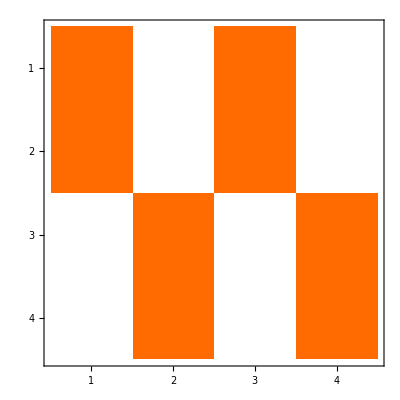

```mathematica
(Transpose[q2c16[[7,{1,3,2,4},#]]]//MatrixPlot)&/@(Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]))
```

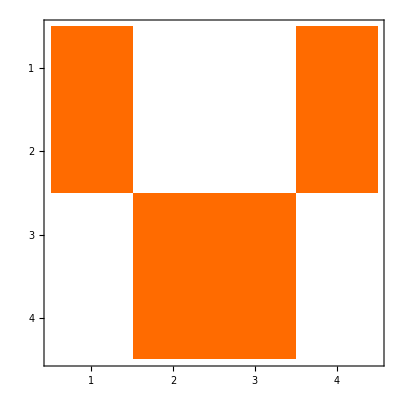
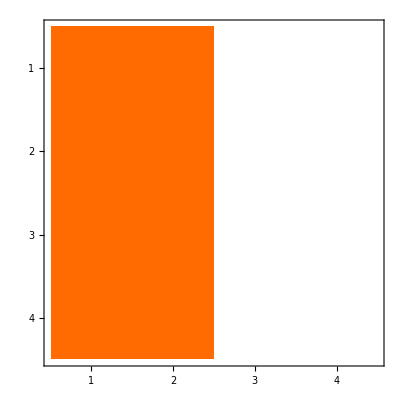

```mathematica
{q2c16[[7]]//MatrixPlot,q2c16[[2,{1,2,3,4},{1,3,2,4}]]//MatrixPlot}
```

## Función para encontrar un elemento representativo

```mathematica
({(Join@@{{1},#}),{1,2,3,4}}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]))
```

{{{1,2,3,4},{1,2,3,4}},{{1,3,4,2},{1,2,3,4}},{{1,4,2,3},{1,2,3,4}}}

```mathematica
first=q2c16[[7]];
Do[
elements=(q2c16[[i,#[[1]],#[[2]]]])&/@({{1,2,3,4},(Join@@{{1},#})}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]));
elements=Join@@{elements,(q2c16[[i,#[[1]],#[[2]]]])&/@({(Join@@{{1},#}),{1,2,3,4}}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]))};
Print[elements];
If[first[[1]]==#&&i≠1,value=i;Break[],Nothing]&/@elements;
,{i,15}]
```

```mathematica
ArrayPlot/@(first[[#[[1]],#[[2]]]]&/@({(Join@@{{1},#}),{1,2,3,4}}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}])))
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@(Transpose[first[[#[[1]],#[[2]]]]]&/@({(Join@@{{1},#}),{1,2,3,4}}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}])))
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Cube3q[q3c32[[15]]//Flatten]
```

-Graphics3D-

```mathematica
Cube3q[#//Flatten]&/@representativos
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{Cube3q[Erase[{representativos[[2]]},{representativos[[1]]},16]//Flatten],Cube3q[Erase[{representativos[[3]]},{representativos[[1]]},16]//Flatten],Cube3q[Erase[{representativos[[4]]},{representativos[[1]]},16]//Flatten],Cube3q[Erase[{representativos[[6]]},{representativos[[1]]},16]//Flatten],Cube3q[Erase[{q3c32[[15]]},{representativos[[3]]},16]//Flatten],Cube3q[Erase[{representativos[[7]]},{representativos[[3]]},16]//Flatten],Cube3q[Erase[{representativos[[7]]},{representativos[[6]]},16]//Flatten]}
```

```mathematica
{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}
```

```mathematica
possible=Tuples[{0,1,3},3];
real={};
Do[
If[Total[#]==i,AppendTo[real,#];Continue[]]&/@possible
,{i,0,16}]
```

```mathematica
real
```

9

```mathematica
648/6/3/3
```

12

```mathematica
(If[Signature[#]==1,#,Nothing]&/@Permutations[{1,2,3}])
```

{{1,2,3},{2,3,1},{3,1,2}}

```mathematica
Cube3q[#//Flatten]&/@(Join@@DeleteDuplicates[{DeleteDuplicates[Transpose[#,{1,2,3}]&/@(Erase[{representativos[[2]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{2,3,1}]&/@(Erase[{representativos[[2]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{3,1,2}]&/@(Erase[{representativos[[2]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])]}])
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(Join@@DeleteDuplicates[{DeleteDuplicates[Transpose[#,{1,2,3}]&/@(Erase[{representativos[[3]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{2,3,1}]&/@(Erase[{representativos[[3]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{3,1,2}]&/@(Erase[{representativos[[3]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])]}])//Length
```

27

```mathematica
(Join@@DeleteDuplicates[{DeleteDuplicates[Transpose[#,{1,2,3}]&/@(Erase[{representativos[[4]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{2,3,1}]&/@(Erase[{representativos[[4]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{3,1,2}]&/@(Erase[{representativos[[4]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])]}])//Length
```

27

```mathematica
(Join@@DeleteDuplicates[{DeleteDuplicates[Transpose[#,{1,2,3}]&/@(Erase[{representativos[[6]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{2,3,1}]&/@(Erase[{representativos[[6]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{3,1,2}]&/@(Erase[{representativos[[6]]},{representativos[[1]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])]}])//Length
```

81

```mathematica
(Join@@DeleteDuplicates[{DeleteDuplicates[Transpose[#,{1,2,3}]&/@(Erase[{representativos[[7]]},{representativos[[3]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{2,3,1}]&/@(Erase[{representativos[[7]]},{representativos[[3]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{3,1,2}]&/@(Erase[{representativos[[7]]},{representativos[[3]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])]}])//Length
```

81

```mathematica
(Join@@DeleteDuplicates[{DeleteDuplicates[Transpose[#,{1,2,3}]&/@(Erase[{representativos[[7]]},{representativos[[6]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{2,3,1}]&/@(Erase[{representativos[[7]]},{representativos[[6]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{3,1,2}]&/@(Erase[{representativos[[7]]},{representativos[[6]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])]}])//Length
```

27

```mathematica
Permutations[{1,2,3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
Cube3q[#//Flatten]&/@(Join@@DeleteDuplicates[{DeleteDuplicates[Transpose[#,{1,2,3}]&/@(Erase[{q3c32[[15]]},{representativos[[3]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{2,3,1}]&/@(Erase[{q3c32[[15]]},{representativos[[3]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{3,1,2}]&/@(Erase[{q3c32[[15]]},{representativos[[3]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{3,2,1}]&/@(Erase[{q3c32[[15]]},{representativos[[3]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],
DeleteDuplicates[Transpose[#,{1,3,2}]&/@(Erase[{q3c32[[15]]},{representativos[[3]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])],DeleteDuplicates[Transpose[#,{2,1,3}]&/@(Erase[{q3c32[[15]]},{representativos[[3]]},16][[1,#[[1]],#[[2]],#[[3]]]]&/@Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3])]}])
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
3+27*3+27+81*3+81*3+27+9*3
```

651

```mathematica
Tuples[Join@@{{1},#}&/@(If[Signature[#]==1,#,Nothing]&/@Permutations[{2,3,4}]),3]
```

{{{1,2,3,4},{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4},{1,3,4,2}},{{1,2,3,4},{1,2,3,4},{1,4,2,3}},{{1,2,3,4},{1,3,4,2},{1,2,3,4}},{{1,2,3,4},{1,3,4,2},{1,3,4,2}},{{1,2,3,4},{1,3,4,2},{1,4,2,3}},{{1,2,3,4},{1,4,2,3},{1,2,3,4}},{{1,2,3,4},{1,4,2,3},{1,3,4,2}},{{1,2,3,4},{1,4,2,3},{1,4,2,3}},{{1,3,4,2},{1,2,3,4},{1,2,3,4}},{{1,3,4,2},{1,2,3,4},{1,3,4,2}},{{1,3,4,2},{1,2,3,4},{1,4,2,3}},{{1,3,4,2},{1,3,4,2},{1,2,3,4}},{{1,3,4,2},{1,3,4,2},{1,3,4,2}},{{1,3,4,2},{1,3,4,2},{1,4,2,3}},{{1,3,4,2},{1,4,2,3},{1,2,3,4}},{{1,3,4,2},{1,4,2,3},{1,3,4,2}},{{1,3,4,2},{1,4,2,3},{1,4,2,3}},{{1,4,2,3},{1,2,3,4},{1,2,3,4}},{{1,4,2,3},{1,2,3,4},{1,3,4,2}},{{1,4,2,3},{1,2,3,4},{1,4,2,3}},{{1,4,2,3},{1,3,4,2},{1,2,3,4}},{{1,4,2,3},{1,3,4,2},{1,3,4,2}},{{1,4,2,3},{1,3,4,2},{1,4,2,3}},{{1,4,2,3},{1,4,2,3},{1,2,3,4}},{{1,4,2,3},{1,4,2,3},{1,3,4,2}},{{1,4,2,3},{1,4,2,3},{1,4,2,3}}}

```mathematica
Cube3q[ThreeQ[[16,#[[1]],#[[2]],#[[3]]]]//Flatten]&/@Flatten[Permutations[{{1,2,3,4},{1,2,3,4},#}]&/@{{1,2,3,4},{1,3,4,2},{1,4,2,3}},1]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Permutations[{{1,2,3,4},{1,2,3,4},{1,2,3,4}}]
```

{{{1,2,3,4},{1,2,3,4},{1,2,3,4}}}

```mathematica
Join@@{ConstantArray[{1,2,3,4},{2}],{{1,2,c,b}}}
```

{{1,2,3,4},{1,2,3,4},{1,2,c,b}}

```mathematica
RowsAndColPermutations[qubits_Integer]:=Flatten[Permutations[Join@@{ConstantArray[{1,2,3,4},{qubits-1}],{#}}]&/@{{1,2,3,4},{1,3,4,2},{1,4,2,3}},1]
```

```mathematica
RowsAndColPermutations[2]
```

{{{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,3,4,2}},{{1,3,4,2},{1,2,3,4}},{{1,2,3,4},{1,4,2,3}},{{1,4,2,3},{1,2,3,4}}}

```mathematica
Flatten[Permutations[{{1,2,3,4},{1,2,3,4},#}]&/@{{1,2,3,4},{1,3,4,2},{1,4,2,3}},1]//Length
```

7

```mathematica
TwoQBoard/@((Transpose[q2c16[[14,#[[1]],#[[2]]]],{1,2}]//Flatten)&/@RowsAndColPermutations[2])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
q3c16//Dimensions
```

{651,4,4,4}

```mathematica
q3c16[[6,;;,1,1]]
```

{1,1,0,0}

```mathematica
q3c16[[6,1,;;,1]]
```

{1,1,1,1}

```mathematica
Position[(Sort[Join@{Tally[#[[;;,1,1]]][[1,2]]-1,Tally[#[[1,;;,1]]][[1,2]]-1,Tally[#[[1,1,;;]]][[1,2]]-1}]&/@q3c16),{0,0,0}]
```

{{486},{487},{490},{491},{501},{503},{505},{507},{517},{518},{521},{522},{546},{547},{554},{555},{561},{563},{569},{571},{577},{578},{585},{586},{610},{611},{614},{615},{625},{627},{629},{631},{641},{642},{645},{646}}

```mathematica
(Sort[Join@{Tally[#[[;;,1,1]]][[1,2]]-1,Tally[#[[1,;;,1]]][[1,2]]-1,Tally[#[[1,1,;;]]][[1,2]]-1}]&/@q3c32)//Tally
```

{{{1,3,3},9},{{1,1,3},27},{{1,1,1},27}}

```mathematica
(Sort[Join@{Tally[#[[;;,1,1]]][[1,2]]-1,Tally[#[[1,;;,1]]][[1,2]]-1,Tally[#[[1,1,;;]]][[1,2]]-1}]&/@q3c8)//Tally
```

{{{0,1,3},18},{{0,1,1},270},{{0,0,3},27},{{1,1,1},27},{{0,0,1},621},{{0,0,0},432}}

```mathematica
(Sort[Join@{Tally[#[[;;,1,1]]][[1,2]]-1,Tally[#[[1,;;,1]]][[1,2]]-1,Tally[#[[1,1,;;]]][[1,2]]-1}]&/@q3c4)//Tally
```

{{{0,0,3},3},{{0,1,1},27},{{0,0,1},216},{{0,0,0},405}}

```mathematica
(Sort[Join@{Tally[#[[;;,1,1]]][[1,2]]-1,Tally[#[[1,;;,1]]][[1,2]]-1,Tally[#[[1,1,;;]]][[1,2]]-1}]&/@q3c2)//Tally
```

{{{0,0,1},9},{{0,0,0},54}}

```mathematica
{{486},{487},{490},{491},{501},{503},{505},{507},{517},{518},{521},{522},{546},{547},{554},{555},{561},{563},{569},{571},{577},{578},{585},{586},{610},{611},{614},{615},{625},{627},{629},{631},{641},{642},{645},{646}}//Flatten
```

{486,487,490,491,501,503,505,507,517,518,521,522,546,547,554,555,561,563,569,571,577,578,585,586,610,611,614,615,625,627,629,631,641,642,645,646}

```mathematica
perm=Permutations[{1,2,3}];
family=Flatten[Position[(Sort[Join@{Tally[#[[;;,1,1]]][[1,2]]-1,Tally[#[[1,;;,1]]][[1,2]]-1,Tally[#[[1,1,;;]]][[1,2]]-1}]&/@q3c8),{0,0,0}]];
AllTrue[Flatten[Table[MemberQ[q3c8[[#]]&/@family,Transpose[q3c8[[#]],perm[[i]]]]&/@family,{i,Length[perm]}],1],TrueQ]
```

True

```mathematica
SparseArray[Position[q2c4,1]->ConstantArray[1,140],{140,4,4}]
```

SparseArray[…]

```mathematica
If[#[[2]]==1,Nothing,If[#[[2]]==4,{#[[1]],2,}]]&/@Position[q2c4,1]
```

{Null,Null,True,Null,Null,Null,Null,True,Null,Null,Null,Null,True,True,True,Null,Null,True,Null,Null,Null,Null,True,Null,Null,Null,Null,True,True,True,Null,Null,True,Null,Null,Null,Null,True,Null,Null,Null,Null,True,True,True,Null,Null,True,Null,Null,Null,Null,Null,Null,Null,Null,True,True,Null,Null,True,Null,Null,True,Null,Null,Null,Null,True,True,True,Null,Null,True,Null,Null,Null,Null,True,Null,Null,True,True,True}

## Aplicación sucesiva de mapas

```mathematica
rho=1/2{1+z,x-I y,x+I y,1-z};rho//MatrixForm
```

((1+z)/2
1/2 (x-ⅈ y)
1/2 (x+ⅈ y)
(1-z)/2)

```mathematica
PCE[{1,0,1,0}].PCE[{1,1,0,0}].rho//FullSimplify//MatrixForm
```

(1/2
0
0
1/2)

```mathematica
Subscript[r, 0,0]=1;Table[Subscript[r, i,j],{i,0,3},{j,0,3}]//Flatten
```

{1,r_(0,1),r_(0,2),r_(0,3),r_(1,0),r_(1,1),r_(1,2),r_(1,3),r_(2,0),r_(2,1),r_(2,2),r_(2,3),r_(3,0),r_(3,1),r_(3,2),r_(3,3)}

```mathematica
PCE[{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}].{1,Subscript[r, 0,1],Subscript[r, 0,2],Subscript[r, 0,3],Subscript[r, 1,0],Subscript[r, 1,1],Subscript[r, 1,2],Subscript[r, 1,3],Subscript[r, 2,0],Subscript[r, 2,1],Subscript[r, 2,2],Subscript[r, 2,3],Subscript[r, 3,0],Subscript[r, 3,1],Subscript[r, 3,2],Subscript[r, 3,3]}//FullSimplify//MatrixForm
```

(1/2 (1+r_(1,1))
1/2 (r_(0,1)-r_(1,0))
1/2 (r_(0,2)+r_(1,3))
1/2 (r_(0,3)-r_(1,2))
1/2 (-r_(0,1)+r_(1,0))
1/2 (1+r_(1,1))
1/2 (-r_(0,3)+r_(1,2))
1/2 (r_(0,2)+r_(1,3))
1/2 (r_(2,0)+r_(3,1))
1/2 (r_(2,1)-r_(3,0))
1/2 (r_(2,2)+r_(3,3))
1/2 (r_(2,3)-r_(3,2))
1/2 (-r_(2,1)+r_(3,0))
1/2 (r_(2,0)+r_(3,1))
1/2 (-r_(2,3)+r_(3,2))
1/2 (r_(2,2)+r_(3,3)))

```mathematica
DiagonalMatrix[{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}].DiagonalMatrix[{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0}].DiagonalMatrix[{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1}].DiagonalMatrix[{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1}].{1,Subscript[r, 0,1],Subscript[r, 0,2],Subscript[r, 0,3],Subscript[r, 1,0],Subscript[r, 1,1],Subscript[r, 1,2],Subscript[r, 1,3],Subscript[r, 2,0],Subscript[r, 2,1],Subscript[r, 2,2],Subscript[r, 2,3],Subscript[r, 3,0],Subscript[r, 3,1],Subscript[r, 3,2],Subscript[r, 3,3]}
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}